```mathematica
Clear[HamiltonianWSM, kList1,kList2,kList3,kList4,kList,dataPlot1,dataPlot2,A,B]
```

```mathematica
HamiltonianWSM[kx_,ky_,kz_,t_,t0_,tz_,m_]= Sqrt[t^2 (Sin[kx]^2 + Sin[ky]^2) + (-m + 2 t0 (2-Cos[kx] - Cos[ky]) + tz Cos[kz])^2]
```

√((-m+2 t0 (2-Cos[kx]-Cos[ky])+tz Cos[kz])^2+t^2 (Sin[kx]^2+Sin[ky]^2))

```mathematica
(** K(π,π,π/2) -> Gamma(0,0,0)-> W(0,0,π/2) -> R(π,0,π/2) -> K **)
```

```mathematica
kList1 = N[Table[{π-b π/100,π-b π/100,π/2-b π/200},{b,0,100}]];
```

```mathematica
kList2 = N[Table[{0,0,b π/200},{b,0,100}]];
```

```mathematica
kList3 = N[Table[{b π/100,0,π/2},{b,0,100}]];
```

```mathematica
kList4 = N[Table[{π,b π/100,π/2},{b,0,100}]];
```

```mathematica
kList = Join[kList1,kList2,kList3,kList4];
```

```mathematica
Dimensions[kList]
```

{404,3}

```mathematica
kList[[1]]
```

{3.14159,3.14159,1.5708}

```mathematica
dataPlot1 = Table[{n,HamiltonianWSM[kList[[n]][[1]],kList[[n]][[2]],kList[[n]][[3]],1,0.5,1,4]},{n,1,Dimensions[kList][[1]]}];
```

```mathematica
dataPlot2 = Table[{n,-HamiltonianWSM[kList[[n]][[1]],kList[[n]][[2]],kList[[n]][[3]],1,0.5,1,4]},{n,1,Dimensions[kList][[1]]}];
```

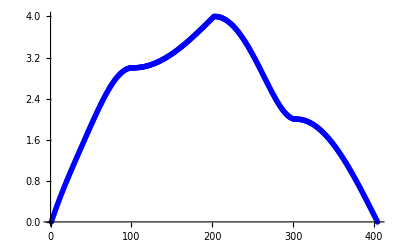

```mathematica
A=ListPlot[dataPlot1,PlotStyle->{PointSize[0.01],Blue}]
```

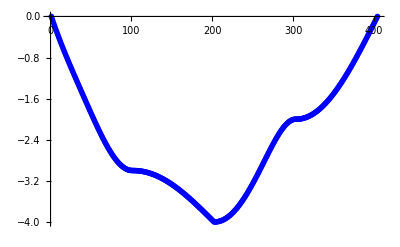

```mathematica
B=ListPlot[dataPlot2,PlotStyle->{PointSize[0.01],Blue}]
```

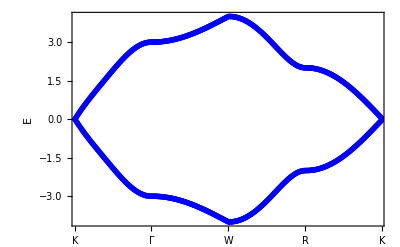

```mathematica
AA = Show[A,B,PlotRange->{{5,398},All},Frame-> True,FrameTicks->{{{1,"K"},{101,"Γ"},{202,"W"},{303,"R"},{403,"K"}},Automatic,None,None}, BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"","E"},RotateLabel->False]
```

```mathematica
kList3Zoomed = N[Table[{π-2+0.02b,0,π/2},{b,0,100}]];
```

```mathematica
kList4Zoomed = N[Table[{π,0.02b,π/2},{b,0,100}]];
```

```mathematica
kListZoomed = Join[kList3Zoomed ,kList4Zoomed] ;
```

```mathematica
dataPlot1Zoomed = Table[{n,HamiltonianWSM[kListZoomed[[n]][[1]],kListZoomed[[n]][[2]],kListZoomed[[n]][[3]],1,0.5,1,0]},{n,1,Dimensions[kListZoomed][[1]]}];
```

```mathematica
dataPlot2Zoomed = Table[{n,-HamiltonianWSM[kListZoomed[[n]][[1]],kListZoomed[[n]][[2]],kListZoomed[[n]][[3]],1,0.5,1,0]},{n,1,Dimensions[kListZoomed][[1]]}];
```

```mathematica
InsetPlot = Show[ListPlot[dataPlot1Zoomed,PlotStyle->{PointSize[0.01],Blue}],ListPlot[dataPlot2Zoomed,PlotStyle->{PointSize[0.01],Blue}],PlotRange->All,Frame-> True,FrameTicks->None,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},ImageSize->50]
```

-Graphics-

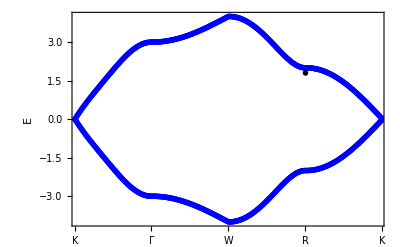

```mathematica
AAA = Show[AA,
 Epilog-> Inset[InsetPlot,{303,1.8}],FrameLabel->{"","E"}]
```